zad 1

p = 0;
q = 6;

indexite zapochvat ot 1

```mathematica
A=({{1+2/3, 0.05, -0.1}, {0.2, 1-1/8, 0}, {0.5, 0, 1+3/10}})
```

{{5/3,0.05,-0.1},{0.2,7/8,0},{0.5,0,13/10}}

```mathematica
B=({{6}, {6}, {1}})
```

{{6},{6},{1}}

```mathematica
LinearSolve[A,B]
```

{{3.38553},{6.08331},{-0.532895}}

```mathematica
(*razgunat vid na matricata A*)
```

#### 5/3 x1+0.05x2-0.1x3=6 0.2x1+7/8 x2+0x3=6 0.5x1+0x2+13/10 x3=1

```mathematica
(*prexvurlqme  vsi4ko koeto e bez xi otdqsno*)
```

x1=0.05/(3/5)x2-0.1/(5/3)x3+6/(5/3)

x2 = 0.2/(7/8)x1+6/(7/8)
x3=0.5/(13/10)x1 + 1/(13/10)

x=C.x +d

```mathematica
CA=({{0, 0.05/(3/5), 0.1/(5/3)}, {0.2/(7/8), 0, 0}, {0.5/(13/10), 0, 0}})
```

{{0,0.0833333,0.06},{0.228571,0,0},{0.384615,0,0}}

```mathematica
d=({{6/(5/3)}, {6/(7/8)}, {1/(13/10)}})
```

{{18/5},{48/7},{10/13}}

```mathematica
{{18/5},{48/7},{10/13}}
```

{{18/5},{48/7},{10/13}}

```mathematica
n=3;(*pravim 3 iteracii*)
```

```mathematica
For[i=1,i≤n,i++,
CA[[i]]=-A[[i]]/A[[i,i]];
CA[[i,i]]=0;
d[[i]]=d[[i]]/A[[i,i]];
]
CA
```

{{0,-0.03,0.06},{-0.228571,0,0},{-0.384615,0,0}}

```mathematica
MatrixForm[CA]
```

(0 | -0.03 | 0.06
-0.228571 | 0 | 0
-0.384615 | 0 | 0)

```mathematica
d
```

{{54/25},{384/49},{100/169}}

```mathematica
MatrixForm[d]
```

(54/25
384/49
100/169)

```mathematica
x0={0,0,0}; (*izbirame nulevo nachalno priblijenie*)
Print["k = ",0, " x^(0) = ",x0];


For[k=1,k≤n,k++,
x1 = CA.x0+d;
eps = Norm[x1-x0];(*predstavqme vuv vid na chislo*)
x0=x1;(*promenqme nachalnoto priblijenie*)
Print["k = ",k, " x^(k) = ",x0, " e^(k) = ",eps]
]
```

k = 0 x^(0) = {0,0,0}

k = 1 x^(k) = {{2.16},{7.83673},{0.591716}} e^(k) = 8.15047

k = 2 x^(k) = {{1.9604},{7.34302},{-0.239053}} e^(k) = 0.986798

k = 3 x^(k) = {{1.92537},{7.38864},{-0.162284}} e^(k) = 0.0959287

```mathematica
x0={0,0,0};
prec = 10^-6;
```

```mathematica
eps=1;
```

```mathematica
For[k=1,eps>prec,k++,
x1 = CA.x0+d;
eps = Norm[x1-x0];(*predstavqme vuv vid na chislo*)
x0=x1;(*promenqme nachalnoto priblijenie*)
Print["k = ",k, " x^(k) = ",x0, " e^(k) = ",eps]
]
```

k = 1 x^(k) = {{2.16},{7.83673},{0.591716}} e^(k) = 8.15047

k = 2 x^(k) = {{1.9604},{7.34302},{-0.239053}} e^(k) = 0.986798

k = 3 x^(k) = {{1.92537},{7.38864},{-0.162284}} e^(k) = 0.0959287

k = 4 x^(k) = {{1.9286},{7.39665},{-0.148809}} e^(k) = 0.0160057

k = 5 x^(k) = {{1.92917},{7.39591},{-0.150055}} e^(k) = 0.00155594

k = 6 x^(k) = {{1.92912},{7.39578},{-0.150273}} e^(k) = 0.000259608

k = 7 x^(k) = {{1.92911},{7.39579},{-0.150253}} e^(k) = 0.000025237

k = 8 x^(k) = {{1.92911},{7.3958},{-0.150249}} e^(k) = 4.21079×10^-6

k = 9 x^(k) = {{1.92911},{7.3958},{-0.15025}} e^(k) = 4.09339×10^-7

```mathematica
Log[prec/(Norm[x0]+Norm[d]/(1-Norm[CA]))]/Log[Norm[CA]]
```

21.0427

```mathematica
21.042698811938756(*minimalniq broi iteracii za tochnost 10^-6  e 22*)
```

21.0427

zad 2

```mathematica
p=0;
q=6;
```

```mathematica
(*lokalicaciq na koren chrez metoda na xordite*)
```

```mathematica
f[x_] :=x^3 -(p+40)Sin[x]-3(q+p+1);
```

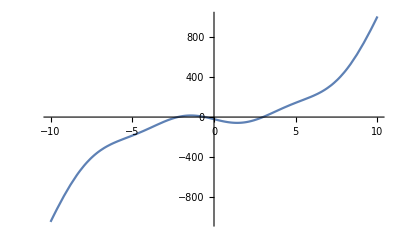

```mathematica
Plot[f[x],{x,-10,10}]
```

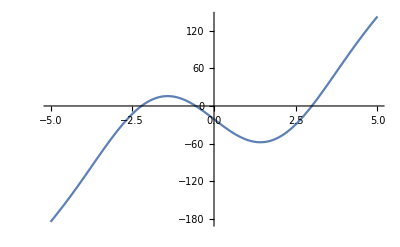

```mathematica
Plot[f[x],{x,-5,5},AxesOrigin->{0,0}]
```

```mathematica
(*broq na korenite e 3*)
```

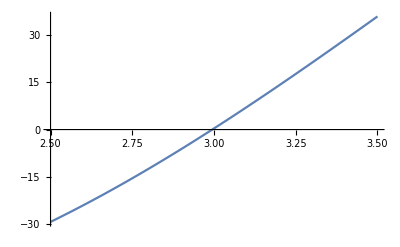

```mathematica
Plot[f[x],{x,2.5,3.5}]
```

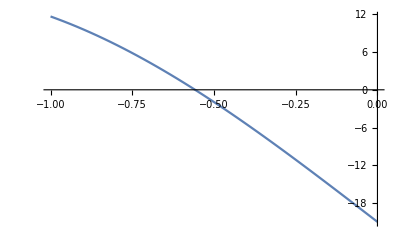

```mathematica
Plot[f[x],{x,-1,0}]
```

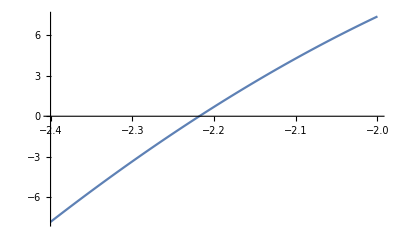

```mathematica
(*lokalizirame nai-malkiq koren*)
Plot[f[x],{x,-2.4,-2}]
```

```mathematica
a=-2.4;b=-2;
```

```mathematica
f[N[a]]
```

-7.80547

```mathematica
f[N[b]]
```

7.3719

имаме корен, защото знакът се променя в дадения интервал

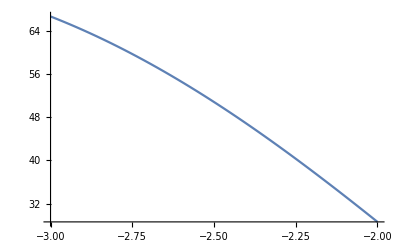

```mathematica
(*proverqvame usloviqta na metoda=>dali f' i f'' sa s postoqnen znak*)
Plot[f'[x],{x,a,b}]
```

izvod: purvata proizvodna e s postoqnen znak (v opredeleniq interval) f’(x)>0

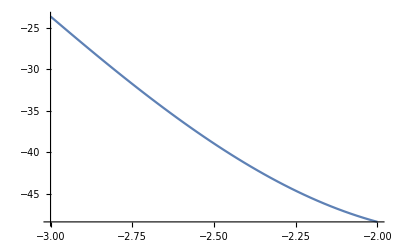

```mathematica
Plot[f''[x],{x,a,b}]
```

izvod : vtorata proizvodna e s postoqnen znak (v opredeleniq interval) f'' (x) < 0

izbirame nachalno priblijenie f(x0).f’’<0   pri f’’<0   x0 trqbva da e >0
izbirame -2 za postoqnna tochka

```mathematica
x0=-2.; (*nachalno priblijenie*)
p = -2.4; (*postoqnna tochka*)

f[x0]
```

12.3896

```mathematica
f[p]
```

-2.22658

```mathematica
m1=Abs[f'[-2.]](*minimum*)
```

27.6471

```mathematica
M1=Abs[f'[-2.4]]
```

45.006

```mathematica
K=(M1 - m1)/m1
```

0.627873

```mathematica
xprev=x0; (*predishna tochka*)
Print["n=0"," x=",x0," f[x]",f[x0]];
For[n=0,n<5,n++,
xnext=xprev - f[xprev]/(f[xprev]-f[p])(xprev-5); (*sledvashtata tochka*)
eps = K*Abs[xnext-xprev]; (*tekushta greshka*)

Print["n=", n+1," x= ",xnext," f[x] ",SetPrecision[f[xnext],14]," eps ", eps];
xprev = xnext;
]
```

n=0 x=-2. f[x]12.3896

n=1 x= 3.93364 f[x] 73.830709004579 eps 3.72557

n=2 x= 4.96878 f[x] 145.24414499176 eps 0.649938

n=3 x= 4.99953 f[x] 147.22522865305 eps 0.0193049

n=4 x= 4.99999 f[x] 147.25510095874 eps 0.000291533

n=5 x= 5. f[x] 147.25554599808 eps 4.34338×10^-6

p=0;
q=6;

f[x_] :=x^3 -(p+40)Sin[x]-3(q+p+1);

zad 3

```mathematica
(*polinomut e ot vtora stepen n=2 => izpolzvame 3 tochki*)
```

```mathematica
xt={-2,1,0,1,2}
```

{-2,1,0,1,2}

```mathematica
yt = Table[f[x],{x,-2,2}]
```

{12.3896,16.8393,-13.8,-44.4393,-39.9896}

```mathematica
s=0.5
```

0.5

```mathematica
xt={0,1,2}
```

{0,1,2}

```mathematica
yt={-13.8,-44.4393,-39.9896}
```

{-13.8,-44.4393,-39.9896}

```mathematica
{-13.8,-44.4393,-39.9896}
```

{-13.8,-44.4393,-39.9896}

```mathematica
xx0 = 0;
xx1=1;
xx2=2;

yy0=-13.8;
yy1=-44.4393;
yy2=-39.9896;
```

```mathematica
L2[x_]:= -13.8*((x-xx1)(x-xx2))/((xx0-xx1)(xx0-xx2)) + -44.4393*((x-xx0)(x-xx2))/((xx1-xx0)(xx1-xx2))  + 39.9896*((x-xx0)(x-xx1))/((xx2-xx0)(xx2-xx1))
```

```mathematica
L2[x]
```

-6.9 (-2+x) (-1+x)+44.4393 (-2+x) x+19.9948 (-1+x) x

```mathematica
Expand[L2[x]] (*dava ni polinoma v kanoni4en vid*)
```

-13.8-88.1734 x+57.5341 x^2

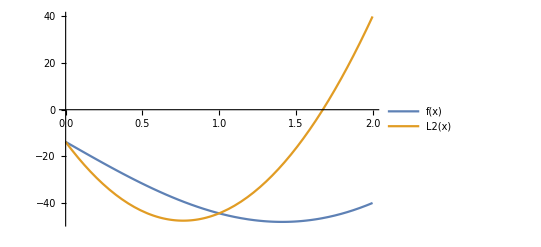

```mathematica
Plot[{f[x],L2[x]},{x,0,2},PlotLegends->"Expressions"] (*intervala ot tablicata*)
```

```mathematica
(*proverqvame usloviqta=>dali suvpadat stoinostite*)
```

```mathematica
L2[0]
```

-13.8

```mathematica
L2[1]
```

-44.4393

```mathematica
L2[2]
```

39.9896

```mathematica
(*namirame priblijenata stoinost na funkciqta v opredelenata tochka*)
```

```mathematica
f[s]
```

-31.7014

```mathematica
L2[s]
```

-43.5032

```mathematica
Print["istinskata greshka e ", Abs[L2[s]-f[s]]]
```

istinskata greshka e 11.8018

zad 4 ODU

```mathematica
a=0;b=0.4;n=4;
```

```mathematica
f[x_,y_]:=Sin[x^2+y]
```

```mathematica
x0=a;
y0=1;
```

```mathematica
h=(b-a)/n;
```

```mathematica
xi=Table[a+i*h,{i,0,n}];(*sustavqme tablicata*)
```

```mathematica
For[i=0;x=x0;y=y0,
 i≤n,i++,
Print["i = ",i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y]];
y=y+h*f[x,y];
x=x+h
 ]
```

i = 0 x_i = 0 y_i = 1 f_i = Sin[1]

i = 1 x_i = 0.1 y_i = 1.08415 f_i = 0.888537

i = 2 x_i = 0.2 y_i = 1.173 f_i = 0.936671

i = 3 x_i = 0.3 y_i = 1.26667 f_i = 0.977162

i = 4 x_i = 0.4 y_i = 1.36438 f_i = 0.998923

```mathematica
Print["globalnata greshka e= ",h]
```

globalnata greshka e= 0.1

```mathematica
Print["lokalnata greshka na izchisleniqta e= ",h^2]
```

lokalnata greshka na izchisleniqta e= 0.01

```mathematica
xi=Table[a+i*h,{i,0,n}];(*sustavqme nova tablica 'mreja'*)
```

```mathematica
For[i=0;x=x0;y=y0,i≤n,i++,
x12=x+1/2 h;
y12=y+h/2 f[x,y];
Print["  i= ",i,"  x= ",x,"  yi= ",y,"  fi= ",f[x,y],
"  x_(i + FractionBox[1, 2]) = ",x12,"  y_(i + FractionBox[1, 2]) = ",y12,"  f_(i + FractionBox[1, 2]) = ",f[x12,y12]];
y=y+h*f[x12,y12];
x=x+h

]
```

i= 0  x= 0  yi= 1  fi= Sin[1]  x_(i + FractionBox[1, 2]) = 0.05  y_(i + FractionBox[1, 2]) = 1.04207  f_(i + FractionBox[1, 2]) = 0.86471

i= 1  x= 0.1  yi= 1.08647  fi= 0.889601  x_(i + FractionBox[1, 2]) = 0.15  y_(i + FractionBox[1, 2]) = 1.13095  f_(i + FractionBox[1, 2]) = 0.914168

i= 2  x= 0.2  yi= 1.17789  fi= 0.938371  x_(i + FractionBox[1, 2]) = 0.25  y_(i + FractionBox[1, 2]) = 1.22481  f_(i + FractionBox[1, 2]) = 0.960085

i= 3  x= 0.3  yi= 1.2739  fi= 0.978672  x_(i + FractionBox[1, 2]) = 0.35  y_(i + FractionBox[1, 2]) = 1.32283  f_(i + FractionBox[1, 2]) = 0.992139

i= 4  x= 0.4  yi= 1.37311  fi= 0.99929  x_(i + FractionBox[1, 2]) = 0.45  y_(i + FractionBox[1, 2]) = 1.42307  f_(i + FractionBox[1, 2]) = 0.9985

```mathematica
Print["lokalnata greshka na izchisleniqta e= ",h^3]
```

lokalnata greshka na izchisleniqta e= 0.001

```mathematica
Print["globalnata greshka e= ",h^2]
```

globalnata greshka e= 0.01